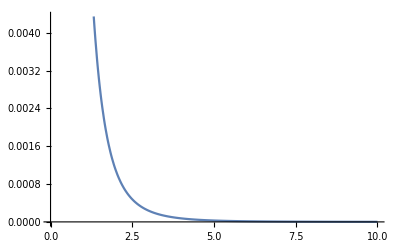

```mathematica
a:=1
b:=1.1
f[r_]:= (-1/(2*a^3*(a-b)^4*b^2*(a+r)^2*(b+r)))*(2*(a-b)^4*(a+r)^2*(b+r)*Log[r]-2*b^2*(6*a^2-4*a*b+b^2)*(a+r)^2*(b+r)*Log[a+r]+a*((a-b)*b*(2*a^4+4*a^3*r-2*b^2*r*(b+r)+3*a*b*(-b^2+b*r+2*r^2)+a^2*(7*b^2+7*b*r+2*r^2))-2*a^2*(a-4*b)*(a+r)^2*(b+r)*Log[b+r]))
Plot[f[r],{r,0,10}]
(*Integrate[f[r],r]*)
```